```mathematica
(*System information*)
```

```mathematica
data = {M->2, m->1, l->3, g->9.81};
```

```mathematica
(*Lagrangian Dynamics Formulation*)
```

```mathematica
KE = Simplify[Expand[1/2*(M*x'[t]^2+m*((D[x[t]-l*Sin[θ[t]], t]^2)+D[l*Cos[θ[t]], t]^2))]];
PE = m*g*l*Cos[θ[t]];
Lagrangian = KE-PE;
```

```mathematica
eq1 = Simplify[D[D[Lagrangian, x'[t]],t]-D[Lagrangian, x[t]]-fcart];
eq2 = Simplify[D[D[Lagrangian, θ'[t]],t]-D[Lagrangian, θ[t]]];
dyn = {x''[t], θ''[t]}/.Solve[{eq1==0, eq2==0}, {x''[t], θ''[t]}][[1]];
dyneqns = Simplify[dyn/.data];
```

```mathematica
(*The systems configuration space belongs to R^1 X S^1*)
```

```mathematica
q = {x, θ};
```

```mathematica
(*Leaving the system with an initial condition and simulating it to see if the dynamics is correct*)
```

```mathematica
(*Initial conditions*)
```

```mathematica
qinit ={0,π/4};
dqinit = {0,0};
```

```mathematica
(*qinit ={0,0+0.0000001};
dqinit = {0, 0};*)
```

```mathematica
dyntesteqns = dyneqns/.fcart->0;
dyntesteqns2 = dyntesteqns/.{θ[t]->θ, x[t]->x, θ'[t]->dθ};
```

```mathematica
doubledots[q_?(VectorQ[#,NumericQ]&), dq_?(VectorQ[#,NumericQ]&)]:=Module[{},
Return[dyntesteqns2/.{θ->q[[2]], dθ->dq[[2]]}]
]
```

```mathematica
dyntestmod = NDSolve[{doubledots[q1[t], q1'[t]]==q1''[t], q1[0]== qinit, q1'[0]==dqinit},q1,{t, 0, 90}][[1]];
qvalsmod = Table[Join[(q1/.dyntestmod)[t], (q1/.dyntestmod)'[t]],{t, 0, 90, 0.01}];
Energyexp = (KE+PE)/.data;
time = Table[t, {t, 0, 90, 0.01}];
Energytestdat = Table[Energyexp/.Inner[Rule, {x[t], θ[t], x'[t], θ'[t]}, qvalsmod[[i]], List], {i, Length[qvalsmod]}];
E1 = ConstantArray[Energytestdat[[1]], Dimensions[Energytestdat]];
```

```mathematica
modE = ListPlot[Transpose[{time, (Energytestdat-E1)/E1}], PlotLabel->"Energy Check", AxesLabel->{"simulation time", "Fractional change in energy"}, PlotRange->All, PlotStyle->{Red}];
```

```mathematica
dyntest = NDSolve[{dyntesteqns[[1]]==x''[t], dyntesteqns[[2]]==θ''[t], {x[0], θ[0]}== qinit, {x'[0], θ'[0]}==dqinit},q,{t, 0, 90}][[1]];
qtestdat = Table[{(x/.dyntest[[1]])[t], (θ/.dyntest[[2]])[t], (x/.dyntest[[1]])'[t], (θ/.dyntest[[2]])'[t]},{t, 0, 90, 0.01}];
Energytestdat = Table[Energyexp/.Inner[Rule, {x[t], θ[t], x'[t], θ'[t]}, qtestdat[[i]], List], {i, Length[qtestdat]}];
E1 = ConstantArray[Energytestdat[[1]], Dimensions[Energytestdat]];
```

```mathematica
nonE = ListPlot[Transpose[{time, (Energytestdat-E1)/E1}], PlotLabel->"Energy Check", AxesLabel->{"simulation time", "Fractional change in energy"}, PlotRange->All];
```

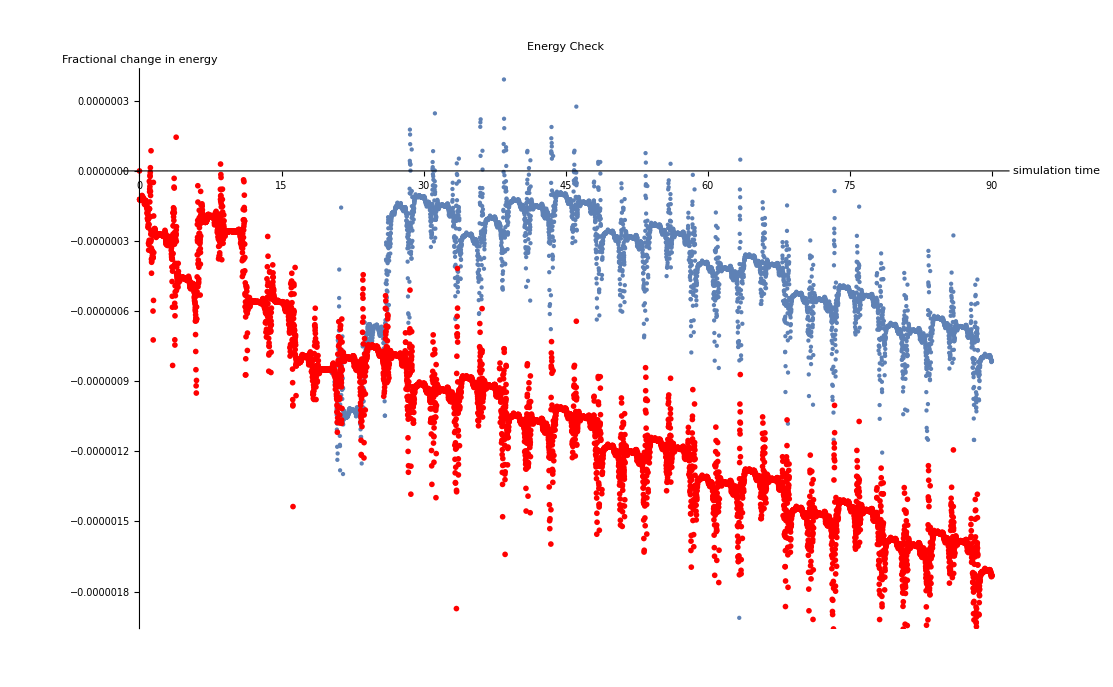

```mathematica
Show[nonE, modE]
```